# Processing perturbation raw data (experiments and FEM)

## Utils

### General

```mathematica
SetDirectory[NotebookDirectory[]];
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
```

### System dependent: labels, system, geometry

```mathematica
(*Get equilibrium angles*)
Clear[eqAngle];
eqAngle[s_String]:=With[{char=StringPart[s, 1]},
Which[
char=="A",-π/4,
char=="B",-3π/4,
char=="C",3π/4,
char=="D",π/4,
char=="x",π/4,(*for xD hyperstatic*)
char=="y",π/4,(*for yD hyperstatic*)
True,$Failed
]
]
eqAngle[___]:=$Failed;

(*Get indices of UC*)
Clear[ucIndex];
(*second character: j, third character: i*)
ucIndex[s_String]:=ToExpression@StringPart[s,{-1,-2}];
ucIndex[___]:=$Failed

(*Get the position of pivot inside UC*)
Clear[pivotPositionsInsideUC];
pivotPositionsInsideUC[s_String,{ax_,ay_}]:=With[{char=StringPart[s, 1]},
Which[
char=="A",{0,0},
char=="B",{0,-ay},
char=="C",{ax,-ay},
char=="D",{ax,0},
char=="x",{ax,0},(*for xD hyperstatic*)
char=="y",{ax,0},(*for yD hyperstatic*)
True,$Failed
]
]
pivotPositionsInsideUC[___]:=$Failed


Clear[pairKeysBeadsFun];
pairKeysBeadsFun[keysBeads_List]:=Module[
{intraPairs,extraPairs,intraF,extraF,s,iMax,jMax},
s=ToString@#&;
iMax=Max[ToExpression@StringPart[#,3]&/@keysBeads];
jMax=Max[ToExpression@StringPart[#,2]&/@keysBeads];

intraF[i_,j_]:=Map[#<>s[j]<>s[i]&,{{"A","B"},{"B","C"},{"C","D"}},{2}];
extraF[i_,j_]:={
{"A"<>s[j+1]<>s[i],"B"<>s[j]<>s[i]},
{"C"<>s[j]<>s[i],"B"<>s[j]<>s[i+1]},
{"D"<>s[j]<>s[i],"A"<>s[j]<>s[i+1]}};

intraPairs=Flatten[Table[intraF[i,j],{i,iMax},{j,jMax}],2];
extraPairs=Flatten[Table[extraF[i,j],{i,iMax},{j,jMax}],2];
(*Delete missing keys*)
DeleteMissing[(intraPairs~Join~extraPairs)/.({x_String,y_String}/;!(MemberQ[keysBeads,x]∧MemberQ[keysBeads,y])):>Missing[]]
];
pairKeysBeadsFun[___]:=$Failed;
```

### Plots

```mathematica
(*List RGB color maps*)
listMagma=;
listViridis=;
listBlue=ToExpression@;
listRed=ToExpression@;

(*Color map functions*)
viridisCM=Blend[RGBColor[#]&/@listViridis,#]&;
viridis2DCM[y_]:=Blend[RGBColor[#]&/@(#+{0,0,y}&/@listViridis),#]&;
magmaCM=Blend[RGBColor[#]&/@listMagma,#]&;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;

(*colorNodes={RGBColor[0.122103, 0.00901808, 0.39826],RGBColor[0.11690625, 0.045921750909090904, 0.4135111818181818],RGBColor[0.1117095, 0.08282542181818181, 0.42876236363636366],RGBColor[0.10651275, 0.11972909272727271, 0.44401354545454547],RGBColor[0.101316, 0.15663276363636364, 0.4592647272727273],RGBColor[0.09611925, 0.19353643454545455, 0.4745159090909091],RGBColor[0.0909225, 0.23044010545454544, 0.48976709090909093],RGBColor[0.08572574999999999, 0.2673437763636363, 0.5050182727272727],RGBColor[0.08523945454545455, 0.2995074545454545, 0.5135622727272727],RGBColor[0.08710838636363637, 0.32930113636363634, 0.5187526818181819],RGBColor[0.08897731818181819, 0.3590948181818182, 0.523943090909091],RGBColor[0.09084624999999999, 0.38888849999999997, 0.5291335],RGBColor[0.09271518181818181, 0.41868218181818184, 0.5343239090909091],RGBColor[0.09458411363636363, 0.44847586363636366, 0.5395143181818182],RGBColor[0.09645304545454544, 0.4782695454545455, 0.5447047272727273],RGBColor[0.10123572727272727, 0.5051384090909091, 0.5472709545454546],RGBColor[0.11184590909090908, 0.5261576363636363, 0.5445888181818181],RGBColor[0.1224560909090909, 0.5471768636363636, 0.5419066818181818],RGBColor[0.13306627272727273, 0.568196090909091, 0.5392245454545455],RGBColor[0.14367645454545455, 0.5892153181818182, 0.5365424090909091],RGBColor[0.15428663636363638, 0.6102345454545455, 0.5338602727272727],RGBColor[0.16489681818181817, 0.6312537727272727, 0.5311781363636363],RGBColor[0.175507, 0.652273, 0.528496],RGBColor[0.1965095909090909, 0.6672641363636364, 0.521146],RGBColor[0.21751218181818183, 0.6822552727272727, 0.513796],RGBColor[0.23851477272727273, 0.6972464090909091, 0.506446],RGBColor[0.25951736363636363, 0.7122375454545454, 0.499096],RGBColor[0.28051995454545453, 0.7272286818181818, 0.491746],RGBColor[0.30152254545454543, 0.7422198181818181, 0.484396],RGBColor[0.32252513636363633, 0.7572109545454545, 0.477046],RGBColor[0.35156081818181817, 0.7692791818181818, 0.4685510909090909],RGBColor[0.38461304545454544, 0.7798859545454545, 0.4594837272727273],RGBColor[0.4176652727272727, 0.7904927272727272, 0.45041636363636367],RGBColor[0.4507175, 0.8010995000000001, 0.441349],RGBColor[0.48376972727272727, 0.8117062727272728, 0.43228163636363637],RGBColor[0.5168219545454545, 0.8223130454545455, 0.42321427272727274],RGBColor[0.5498741818181818, 0.8329198181818183, 0.4141469090909091],RGBColor[0.5874953636363637, 0.8426129090909091, 0.40549063636363636],RGBColor[0.6342544545454546, 0.8504786363636364, 0.3976565454545455],RGBColor[0.6810135454545454, 0.8583443636363637, 0.38982245454545456],RGBColor[0.7277726363636363, 0.866210090909091, 0.3819883636363637],RGBColor[0.7745317272727272, 0.8740758181818182, 0.37415427272727275],RGBColor[0.8212908181818181, 0.8819415454545455, 0.3663201818181818],RGBColor[0.8680499090909091, 0.8898072727272728, 0.35848609090909095],RGBColor[0.914809, 0.897673, 0.350652]};*)
colorNodes=With[{n=45},viridisCM[(#-1)/(n-1)]&/@Range[n]];
colorSprings=With[{n=59},viridisCM[(#-1)/(n-1)]&/@Range[n]];
colorPerturbations={RGBColor[0., 0., 0.],RGBColor[0.04066832727272728, 0.014814545454545459, 0.055254872727272746],RGBColor[0.08133665454545456, 0.029629090909090917, 0.11050974545454549],RGBColor[0.12200498181818183, 0.04444363636363637, 0.16576461818181823],RGBColor[0.16267330909090913, 0.059258181818181835, 0.22101949090909098],RGBColor[0.2033416363636364, 0.07407272727272729, 0.2762743636363637],RGBColor[0.24400996363636365, 0.08888727272727275, 0.33152923636363646],RGBColor[0.28467829090909097, 0.1037018181818182, 0.3867841090909092],RGBColor[0.32534661818181826, 0.11851636363636367, 0.44203898181818196],RGBColor[0.3660149454545455, 0.13333090909090914, 0.4972938545454547],RGBColor[0.4105651818181819, 0.14707418181818185, 0.48507345454545453],RGBColor[0.4558918000000001, 0.16060320000000003, 0.45935799999999993],RGBColor[0.5012184181818182, 0.1741322181818182, 0.43364254545454545],RGBColor[0.5465450363636364, 0.18766123636363638, 0.40792709090909085],RGBColor[0.5918716545454547, 0.20119025454545458, 0.3822116363636363],RGBColor[0.6371982727272729, 0.21471927272727276, 0.35649618181818177],RGBColor[0.6825248909090911, 0.22824829090909093, 0.3307807272727272],RGBColor[0.7278515090909092, 0.24177730909090914, 0.3050652727272727],RGBColor[0.7731781272727274, 0.25530632727272734, 0.2793498181818181],RGBColor[0.8021844545454546, 0.2737542545454546, 0.2548038109090908],RGBColor[0.8230306363636364, 0.29466163636363646, 0.2308425272727272],RGBColor[0.8438768181818183, 0.31556901818181826, 0.20688124363636354],RGBColor[0.8647230000000001, 0.3364764000000001, 0.18291995999999988],RGBColor[0.8855691818181819, 0.3573837818181819, 0.15895867636363625],RGBColor[0.9064153636363637, 0.37829116363636367, 0.13499739272727268],RGBColor[0.9272615454545455, 0.3991985454545455, 0.11103610909090902],RGBColor[0.9481077272727274, 0.42010592727272733, 0.0870748254545454],RGBColor[0.9689539090909092, 0.44101330909090913, 0.06311354181818174],RGBColor[0.980501890909091, 0.4640790545454546, 0.05542225090909094],RGBColor[0.9827516727272728, 0.4893031636363637, 0.06400095272727276],RGBColor[0.9850014545454546, 0.5145272727272728, 0.07257965454545458],RGBColor[0.9872512363636364, 0.5397513818181819, 0.0811583563636364],RGBColor[0.9895010181818182, 0.564975490909091, 0.08973705818181824],RGBColor[0.9917508, 0.5901996000000002, 0.09831576000000006],RGBColor[0.9940005818181818, 0.6154237090909093, 0.10689446181818188],RGBColor[0.9962503636363637, 0.6406478181818184, 0.1154731636363637],RGBColor[0.9985001454545455, 0.6658719272727274, 0.12405186545454552],RGBColor[1., 0.689944290909091, 0.1429100181818185],RGBColor[1., 0.7117131636363638, 0.18232707272727303],RGBColor[1., 0.7334820363636365, 0.22174412727272758],RGBColor[1., 0.7552509090909092, 0.2611611818181821],RGBColor[1., 0.777019781818182, 0.3005782363636366],RGBColor[1., 0.7987886545454547, 0.3399952909090912],RGBColor[1., 0.8205575272727275, 0.3794123454545457],RGBColor[1., 0.8423264, 0.4188294]};
optionsListPlot={Joined->True,Frame->True,ImageSize->500,PlotRange->All,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
optionsContourListPlot={Contours->20,ContourShading->True,ContourStyle->None,ColorFunction->magmaCM,ImageSize->500,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
viridis2DCM[y_]:=Blend[RGBColor[#]&/@(#+{0.4y,0.1y,0.4y}&/@listViridis),#]&;
```

## Folder selection: FEM or experiment

```mathematica
pathFEM[node_String]:="../rawData/2DMetamaterial/FEM - perturbations/20211015_hoti_FEM_perturbation_4by3_output/211015_hoti_perturbation_"<>node<>".xlsx";
pathEXP[node_String]:="../rawData/2DMetamaterial/Experiments - perturbations/20220622_Hoti_EXP_all/Output data/20220622_output_data_"<>node<>".xlsx";
pathEXPCornerState[node_String]:="../raw data/2DMetamaterial/Experiments - lowest mode/20230206_output_data_hoti_shaking.xlsx";
perturbedNodesF["FEM"]={"A11","A12","A13","A14","A21","A22","A23","A24","A31","A32","A33","A34","B11","B12","B13","B14","B21","B22","B23","B24","B31","B32","B33","B34","C11","C12","C13","C14","C21","C22","C23","C24","C31","C32","C33","C34","D11","D12","D13","D21","D22","D23","D31","D32","D33","p_D11","p_D12","p_D13","p_D21","p_D22","p_D23","p_D31","p_D32","p_D33"};
perturbedNodesF["EXP"]={"A11","A12","A13","A14","A21","A22","A23","A24","A31","A32","A33","A34","B11","B12","B13","B14","B21","B22","B23","B24","B31","B32","B33","B34","C11","C12","C13","C14","C21","C22","C23","C24","C31","C32","C33","C34","D11_1","D12_1","D13_1","D21_1","D22_1","D23_1","D31_1","D32_1","D33_1","D11_2","D12_2","D13_2","D21_2","D22_2","D23_2","D31_2","D32_2","D33_2"};
perturbedNodesF[___]=$Failed;
thresholdEXP=0.6;
thresholdFEM=0.01;
```

```mathematica
path=pathEXP;
perturbedNodes=perturbedNodesF["EXP"];
threshold=thresholdEXP;
```

## Geometrical parameters at equilibrium

### Importing one dataset to fix the geometry

```mathematica
rawdata=Import[path["A22"],"Data"];
timeRange=10^3 rawdata[[1,2;;,1]];
dt=10^3(rawdata[[1,4,1]]-rawdata[[1,3,1]]);
```

```mathematica
keysBeads=StringTake[#,;;3]&/@rawdata[[2,1,2;;]];
pairsKeyBeads=pairKeysBeadsFun[keysBeads];
```

```mathematica
positionsBeads=With[{r=(1.2 15.) √2,ax=1.2 50.,ay=1.2 50.},
({2ax,-2ay}(ucIndex[#]-{1,1})+pivotPositionsInsideUC[#,{ax,ay}]+r AngleVector[eqAngle[#]])&/@keysBeads];
```

```mathematica
positionsBeadsDS=<|MapThread[#1->#2&,{keysBeads,positionsBeads}]|>;
```

```mathematica
positionsSprings=(positionsBeadsDS[#[[1]]]+positionsBeadsDS[#[[2]]])/2&/@pairsKeyBeads;
```

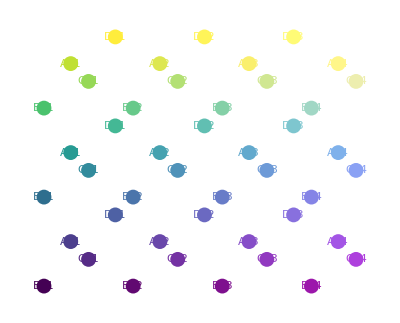

```mathematica
{xmin,xmax}=MinMax[positionsBeads[[All,1]]];
{ymin,ymax}=MinMax[positionsBeads[[All,2]]];
Graphics[MapThread[{viridis2DCM[1+(#1[[1]]-xmax)/(xmax-xmin)][1+(#1[[2]]-ymax)/(ymax-ymin)],Disk[#1,10],Text[#2,#1]}&,{positionsBeads,keysBeads}]]
colorNodes=viridis2DCM[1+(#1[[1]]-xmax)/(xmax-xmin)][1+(#1[[2]]-ymax)/(ymax-ymin)]&/@(positionsBeadsDS[StringTake[#,3]]&/@(perturbedNodesF["EXP"]));
```

## Importing data

### One data set

```mathematica
rawdata=Import[path["A22"],"Data"];
(*reshaping data structure*)
displacementData=#ᵀ&/@(rawdataᵀ[[2;;,All,2;;]]);
```

```mathematica
(*norm of the displacements as a function of time*)
normDispList=Norm@#&/@#&/@displacementData;
```

```mathematica
barl=BarLegend[{viridisCM[#]&,{1,45}},43,LegendLabel->"Node number",LabelStyle->Directive[Black,FontSize->14]];
axesl={"t (ms)","|Displacement| (mm)"};
plotLabel="Perturbation on the 1st node";
ListPlot[{dt Range[0,Length[normDispList]-1],#}ᵀ&/@(normDispListᵀ),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLegends->barl,FrameLabel->axesl,PlotLabel->plotLabel]
```

-Graphics-

```mathematica
pairsIndices=Map[Position[keysBeads,#1][[1,1]]&,pairsKeyBeads,{2}];
elongationData=Table[
Norm[(positionsBeads[[pairIndex[[1]]]]+#[[pairIndex[[1]]]])-(positionsBeads[[pairIndex[[2]]]]+#[[pairIndex[[2]]]])]-Norm[(positionsBeads[[pairIndex[[1]]]])-(positionsBeads[[pairIndex[[2]]]])],{pairIndex,pairsIndices}]&/@displacementData;
```

```mathematica
barl=BarLegend[{viridisCM[#]&,{1,59}},57,LegendLabel->"Spring number",LabelStyle->Directive[Black,FontSize->14]];
axesl={"t (ms)","Elongation (mm)"};
plotLabel="Perturbation on the 1st node";
ListPlot[{dt Range[0,Length[normDispList]-1],#}ᵀ&/@(elongationDataᵀ),Evaluate[optionsListPlot],PlotStyle->colorSprings,PlotLegends->barl,FrameLabel->axesl,PlotLabel->plotLabel]
```

-Graphics-

### All the dataset

```mathematica
displacementDataList=Table[With[{data=Import[path[node],"Data"]},
#ᵀ&/@(dataᵀ[[2;;,All,2;;]])],{node,perturbedNodes}];
```

```mathematica
pairsIndices=With[{auxDS=PositionIndex[keysBeads]},Map[auxDS[[#,1]]&,pairsKeyBeads,{2}]];
elongationDataList=Table[Table[
Norm[(positionsBeads[[pairIndex[[1]]]]+#[[pairIndex[[1]]]])-(positionsBeads[[pairIndex[[2]]]]+#[[pairIndex[[2]]]])]-Norm[(positionsBeads[[pairIndex[[1]]]])-(positionsBeads[[pairIndex[[2]]]])],{pairIndex,pairsIndices}]&/@displacementDataList[[j]],{j,1,Length@displacementDataList}];
```

## Processing the data

### Displacements and elongations

```mathematica
normDispList=Norm@#&/@#&/@#&/@displacementDataList;
```

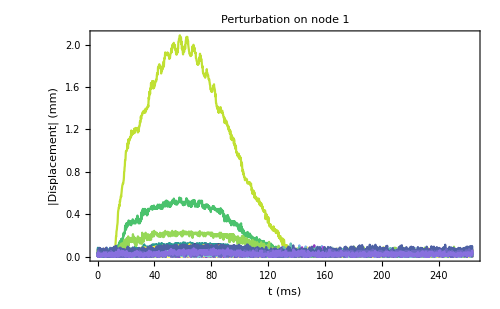

```mathematica
node=1;
(*barl=BarLegend[{viridisCM[#]&,{1,45}},43,LegendLabel->"Node number",LabelStyle->Directive[Black,FontSize->14]];*)
axesl={"t (ms)","|Displacement| (mm)"};
plotLabel="Perturbation on node "<>ToString[node];
ListPlot[With[{tRange=dt Range[0,Length[normDispList[[node]]]-1]},{tRange,#}ᵀ&/@(normDispList[[node]]ᵀ)],Evaluate[optionsListPlot],PlotStyle->colorNodes,FrameLabel->axesl,PlotLabel->plotLabel(*,PlotLegends->barl,*)]
```

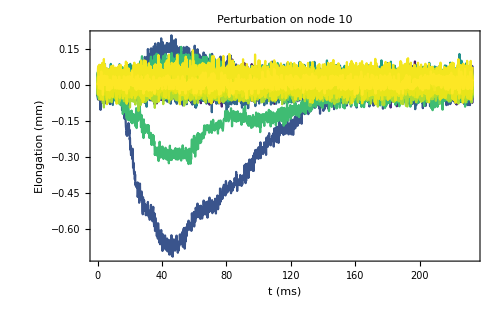

```mathematica
node=10;
(*barl=BarLegend[{viridisCM[#]&,{1,59}},57,LegendLabel->"Spring number",LabelStyle->Directive[Black,FontSize->14]];*)
axesl={"t (ms)","Elongation (mm)"};
plotLabel="Perturbation on node "<>ToString[node];
ListPlot[With[{tRange=dt Range[0,Length[elongationDataList[[node]]]-1]},{tRange,#}ᵀ&/@(elongationDataList[[node]]ᵀ)],Evaluate[optionsListPlot],PlotStyle->colorSprings,FrameLabel->axesl,PlotLabel->plotLabel(*,PlotLegends->barl*)]
```

### Moments

#### Normalized moments and spreading

```mathematica
positionsBeadsExtended=Flatten[ConstantArray[#,2]&/@positionsBeads,1];
flatDisplacementDataList=Map[Flatten[#]&,displacementDataList,{2}];
momentsList=Quiet@MapThread[MapThread[With[{norm2=(#1*.#1+#2*.#2)},
{
Sqrt[norm2],
(#1*.#1-#2*.#2)/norm2,
1/norm2(#1*.(positionsBeadsExtended[[All,1]]#1)+#2*.(positionsSprings[[All,1]]#2)),
1/norm2(#1*.(positionsBeadsExtended[[All,2]]#1)+#2*.(positionsSprings[[All,2]]#2)),
1/norm2(#1*.(positionsBeadsExtended[[All,1]]#1)-#2*.(positionsSprings[[All,1]]#2)),
1/norm2(#1*.(positionsBeadsExtended[[All,2]]#1)-#2*.(positionsSprings[[All,2]]#2))
}]&,{#1,#2}]&,{flatDisplacementDataList,elongationDataList}];
spreadingList=Quiet@MapThread[MapThread[With[{norm2=(#1*.#1+#2*.#2)},
{
Sqrt[norm2],
Sqrt[1/norm2(#1*.(positionsBeadsExtended[[All,1]]^2#1)+#2*.(positionsSprings[[All,1]]^2#2))-1/norm2^2(#1*.(positionsBeadsExtended[[All,1]]#1)+#2*.(positionsSprings[[All,1]]#2))^2],
Sqrt[1/norm2(#1*.(positionsBeadsExtended[[All,2]]^2#1)+#2*.(positionsSprings[[All,2]]^2#2))-1/norm2^2(#1*.(positionsBeadsExtended[[All,2]]#1)+#2*.(positionsSprings[[All,2]]#2))^2]
}]&,{#1,#2}]&,{flatDisplacementDataList,elongationDataList}];
```

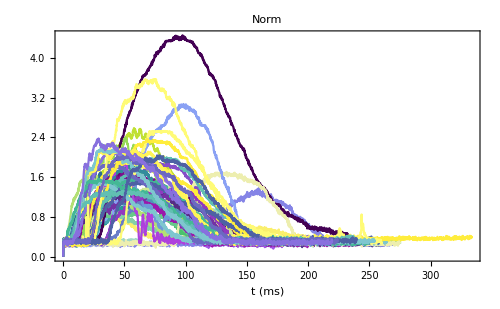
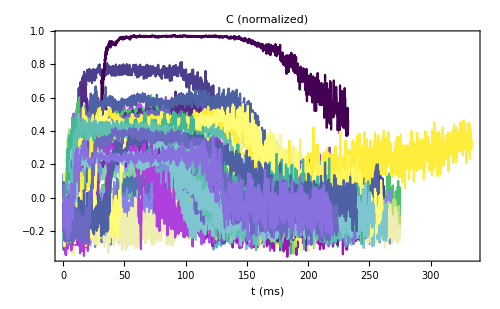
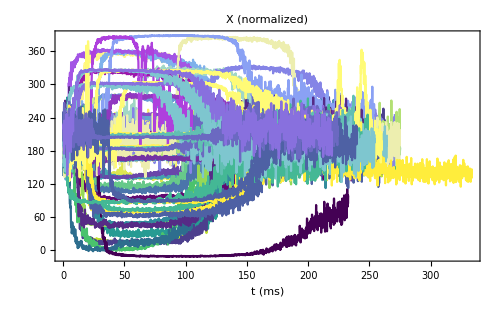
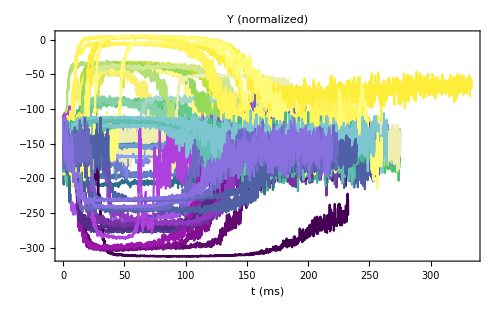
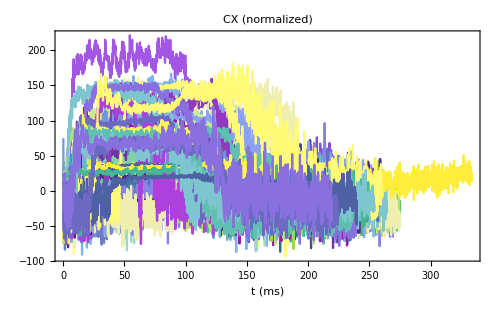
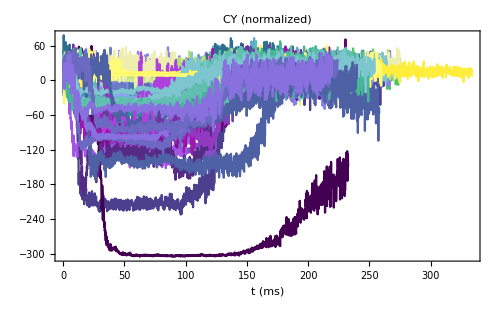

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Mahalanobis distance

Notice that the first data set (at t=0) may trigger a warning for the WeightedData function

```mathematica
weightsInTime=MapThread[MapThread[((Norm@#&/@(#1))^2)~Join~((Abs@#2)^2)&,{#1,#2}]&,{displacementDataList[[All]],elongationDataList[[All]]}];
positions=positionsBeads~Join~positionsSprings;
weightedDataList=(WeightedData[positions,#]&/@#)&/@weightsInTime;
mahalanobisDistanceList=(With[{cov=Covariance[#],mean=Mean[#]},(√((#-mean).(Inverse[cov].(#-mean)))&/@positions)]&/@#)&/@weightedDataList;
```

WeightedData::wtmsg: The argument {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«94»} is not a valid weight specification.

General::stop: Further output of WeightedData::wtmsg will be suppressed during this calculation.

Covariance::arg1: The first argument must be either a vector, a matrix, or a multivariate distribution.

General::stop: Further output of Covariance::arg1 will be suppressed during this calculation.

```mathematica
distanceThreshold=1.2;
pickConfidenceList=((#<distanceThreshold)&/@#&/@#)&/@mahalanobisDistanceList;
```

#### Filter data according to norm

```mathematica
pickList=(#>threshold&/@(#[[All,1]]))&/@momentsList;
momentsList=MapThread[Pick[#1,#2]&,{momentsList,pickList}];
pickConfidenceList=MapThread[Pick[#1,#2]&,{pickConfidenceList,pickList}];
```

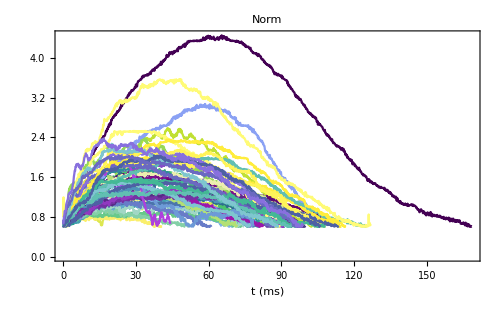
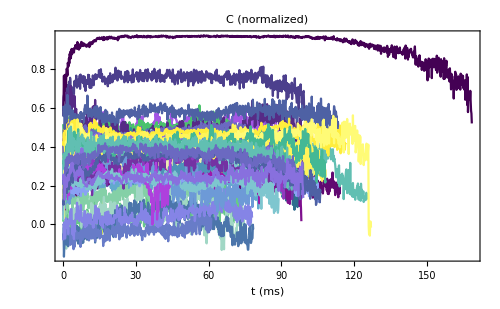
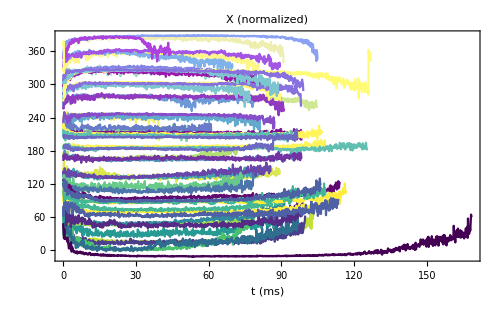
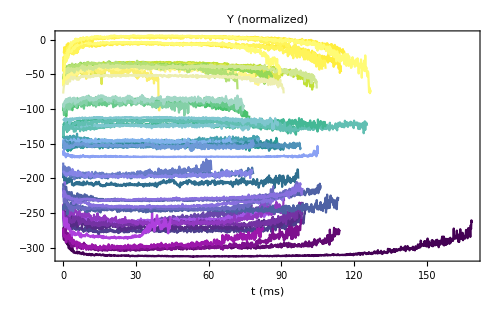
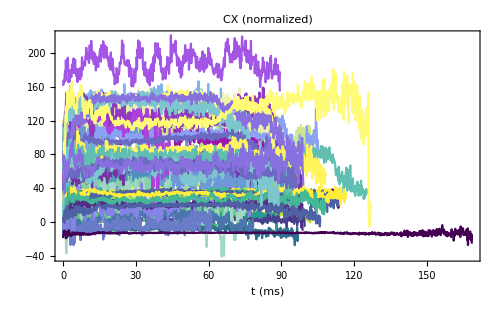
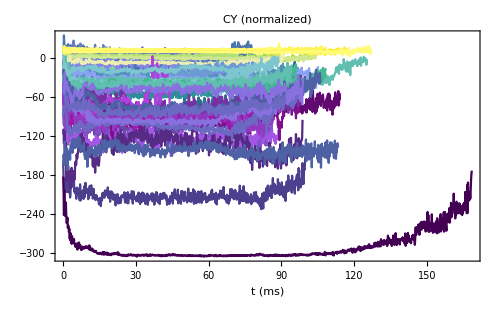

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Field time data

```mathematica
fieldTimeData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList,{2}];
timeList=dt Range[0,Length[#1]-1]&/@fieldTimeData;
```

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Evolution of centers

```mathematica
centers=Flatten[fieldTimeData[[All,All,{1,2}]],1];
Graphics[Disk[#,2]&/@centers]
```

-Graphics-

```mathematica
beadSpringsGraphics=Graphics[{{Red,Disk[#,5]&/@positionsBeads},{Blue,Disk[#,5]&/@positionsSprings}}];
```

```mathematica
polygons2Dcolorless=Table[MapThread[With[{pts=Pick[positions,#]},If[Length@pts>1,If[CollinearPoints@pts,Nothing,{Opacity[0.01],EdgeForm[],ConvexHullMesh[pts]}],Nothing]]
&,{pickConfidenceList[[i]],timeList[[i]]}],{i,1,Length@pickConfidenceList}];
```

```mathematica
Graphics[polygons2Dcolorless]
```

-Graphics-

```mathematica
from={1,13,25,37};
to={12,24,36,-1};
colorMolecules=ColorData["Rainbow"][#]&/@Range[0,0.75,0.25];
MapThread[Show[beadSpringsGraphics,Graphics[{#3,polygons2Dcolorless[[#1;;#2]]}],Graphics[{#3,EdgeForm[{Thickness[0.002],White}],Disk[#,2]&/@Flatten[fieldTimeData[[#1;;#2,All,{1,2}]],1]}]]&,{from,to,colorMolecules}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
refGraphicsMolecules=Show[MapThread[Graphics[{#3,polygons2Dcolorless[[#1;;#2]]}]&,{from,to,colorMolecules}]];
refGraphicsCenters=Show[MapThread[Graphics[{#3,EdgeForm[{Thickness[0.002],White}],Disk[#,2]&/@Flatten[fieldTimeData[[#1;;#2,All,{1,2}]],1]}]&,{from,to,colorMolecules}]];
refGraphicsMoleculesAndCenters=Show[beadSpringsGraphics,refGraphicsMolecules,refGraphicsCenters];
```

#### Time averages

```mathematica
increasingAverageList[l_List]:=Module[{previous,current},previous=0;Table[current=(previous (i-1)+l[[i]])/i;previous=current;current,{i,1,Length@l}]]
```

```mathematica
iFrame=1;
timeAverageDataList=increasingAverageList[#]&/@(fieldTimeData[[All,iFrame;;,#]])&/@Range[4];
```

```mathematica
labelPlots={"X","Y","Π_x","Π_y"};
axesl={"Δ_t(ms)","mm"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(timeAverageDataList[[#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,FrameLabel->axesl,PlotLabel->labelPlots[[#]]]&/@Range[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*EXP*)
nFramesAverage=190;
(*FEM*)
(*nFramesAverage=50;*)
meanAroundDataList=MeanAround[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
meanDataList=Mean[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
stdDataList=StandardDeviation[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
(*Attention: this is the angle of the means*)
meanAroundAngleList=ArcTan@@#&/@(meanAroundDataList[[3;;4]]ᵀ);
```

#### Definition of chiral molecules

If the regions are already computed skip the cell and import the molecules.

```mathematica
regionList={};
DynamicModule[{delimiters={}},
Row@{ClickPane[Show[{refGraphicsMoleculesAndCenters(*contourPlotspd,refImage*),Graphics[{Red,Line[Dynamic[delimiters]]}],Graphics[{Opacity[0.5],Blue,Dynamic@regionList}]},ImageSize->Large],AppendTo[delimiters,#1]&],Button["addMolecule",{AppendTo[regionList,Polygon[delimiters]],delimiters={}}]}
]
```

To export the molecules

```mathematica
(*Export["molecules.mx",regionList]*)
```

To import the molecules

```mathematica
regionList=Import["moleculesMechanicalHOTI-EXP-FromPolygonsAndColors-v2.mx"];
```

```mathematica
Show[beadSpringsGraphics,Graphics[{Opacity[0.5],Black,regionList}]]
```

-Graphics-

#### Coarse-grained field

```mathematica
rmemberfList=RegionMember[#]&/@regionList;
whichCell[{x_,y_}]:=Module[{i,isMember},
i=1;
isMember=rmemberfList[[i]][{x,y}];
While[isMember==False &&i<=Length@regionList,isMember=rmemberfList[[i]][{x,y}];i++];
If[isMember,i,Nothing]
]
```

```mathematica
groupByDistanceTimeAverageData=Gather[meanDataListᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];(*moleculeCentersAndPols=Mean[#]&/@groupByDistance;*)
coarseGrainedField=({Mean[#[[1]]],Mean[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&@(#ᵀ))&/@groupByDistanceTimeAverageData;
```

```mathematica
groupByDistanceTimeSTDPolData=Gather[(meanDataList[[{1,2}]]~Join~(stdDataList[[{3,4}]]))ᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedSTDPolData=(Sqrt[(#.#)/Length[#]^2]&/@(#[[All,{3,4}]]ᵀ))&/@groupByDistanceTimeSTDPolData;
```

```mathematica
coarseGrainedMeanAngles=ArcTan@@#&/@(coarseGrainedField[[All,{3,4}]]);
```

```mathematica
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
coarseGrainedSTDAngleData=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{coarseGrainedField[[All,{3,4}]],coarseGrainedSTDPolData}];
```

### Graphics

#### Full representation

```mathematica
customColorF =  &;
colorDisk = With[ ];
```

```mathematica
colorDisk
```

-Graphics-

```mathematica
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{customColorF[Mod[1 + #2/(2 π) + 0.2, 1]],Thickness[0.01],Arrow[{center-pol/2,center+pol/2}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

```mathematica
Graphics[primitivesList]
```

-Graphics-

#### Fixed-length representation

```mathematica
fcolor=GrayLevel[(35-#)/35]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.01],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.005],Circle[center,circleRadius],Thickness[0.02],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

```mathematica
Graphics[primitivesList]
```

-Graphics-

```mathematica
GraphicsRow[{Graphics[primitivesList],barl}]
```

-Graphics-